# 3

## PHAS2443: Practical Mathematics II Lecture 3: Finite Difference Methods

In the previous lecture we used one of the key ideas of this lecture, when we used the difference between adjacent cells to form an approximation to the gradient of a function. We also showed how we could model complex systems with simple rules linking the behaviour of discrete cells is space. In this lecture we adopt a more conventional approach to the solution of differential equations using finite difference methods. In the course of this we shall explore the problems of stability and accuracy that are crucial in selecting a method. The mathematical methods used in Mathematica implement much more sophisticated methods than those we shall discuss here -- but in some cases, and for large systems, it may be better to construct ones own functions.

## Finite differences for ordinary derivatives

Finite difference methods are based on Taylor's theorem, that a continuous function f(x) can be expanded about some point X as
   f(X+h)=f(X)+h f'(X)+h^2/(2!)f''(X) + h^3/(3!)f'''(X) + ....h^n/(n!)(f`)^(n)(X) + R_(n+1)
   where the truncation error R_(n+1) can always be expressed in the form
   R_(n+1)= h^(n+1)/((n+1)!)f^(n+1)(ξ)
   where ξ is in the range X≤ξ≤X+h for h>0.
   We can rewrite this expression as
   f'(X)=(f(X+h)-f(X))/h - h/(2!)f''(X) - h^2/(3!)f'''(X) - ....
   which shows two things:
     a) as h becomes small, the finite difference approximation becomes a better approximation to the derivative;
     b) the error decreases linearly with h -- it is a first-order approximation, and the error is usually written in the form O(h), for 'of order h'.
    This approximation is called a forward difference approximation, as it finds the slope at X from the value of the function at X and the value at a larger value of x.   Another first-order approximation may be found by taking a backward difference:
     f'(X)=(f(X)-f(X-h))/h + h/(2!)f''(X) - h^2/(3!)f'''(X) + ....
     For a better approximation, consider the slope of the line between X-h and X+h:
      f(X-h)=f(X)-h f'(X)+h^2/(2!)f''(X) - h^3/(3!)f'''(X) + ....
      f(X+h)=f(X)+h f'(X)+h^2/(2!)f''(X) + h^3/(3!)f'''(X) + ....
     and if we subtract and rearrange we find
      f'(X)=(f(X+h)-f(X-h))/(2h)  - h^2/(3!)f'''(X) - ....
      so that this central difference approximation has an error of order h^2, as you should have found in last week's exercises.
      
        We demonstrate the difference approximations on a function representing a beating wave.

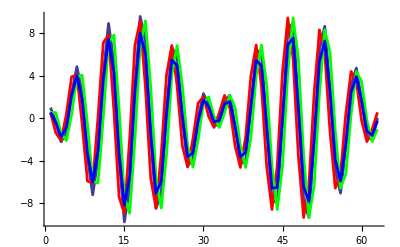

```mathematica
h=0.1;
ft=Table[Sin[x] Cos[10 x],{x,0,2 π,h}];
dft=Table[D[(Sin[x] Cos[10 x]), x]/.x->xp,{xp,0,2 π,h}];
p1=ListPlot[dft,Joined->True,PlotStyle->Thickness[0.005],DisplayFunction->Identity];
pf=ListPlot[(RotateLeft[ft]-ft)/h,Joined->True,PlotStyle->{RGBColor[1,0,0],Thickness[0.005]}];
pb=ListPlot[(ft-RotateRight[ft])/h,Joined->True,PlotStyle->{RGBColor[0,1,0],Thickness[0.005]}];
pc=ListPlot[(RotateLeft[ft]-RotateRight[ft])/(2 h),Joined->True,PlotStyle->{RGBColor[0,0,1],Thickness[0.005]}];
Show[p1,pf,pb,pc]
```

Try looking at the error in the derivative, with h=0.1 and h=0.01.

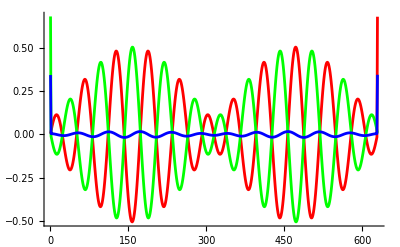

```mathematica
h=0.01;
ft=Table[Sin[x] Cos[10 x],{x,0,2 π,h}];
dft=Table[D[(Sin[x] Cos[10 x]), x]/.x->xp,{xp,0,2 π,h}];
pf=ListPlot[dft-(RotateLeft[ft]-ft)/h,Joined->True,PlotStyle->{RGBColor[1,0,0],Thickness[0.005]}];
pb=ListPlot[dft-(ft-RotateRight[ft])/h,Joined->True,PlotStyle->{RGBColor[0,1,0],Thickness[0.005]}];
pc=ListPlot[dft-(RotateLeft[ft]-RotateRight[ft])/(2 h),Joined->True,PlotStyle->{RGBColor[0,0,1],Thickness[0.005]}];
Show[pf,pb,pc]
```

## First-order differential equations

### Euler's method

Euler's method is a completely straightforward application of a finite difference scheme. To solve the first-order differential equation
  dy/dx= f(x,y)
with the boundary condition y=y_0 at x=x_0, approximate with small steps h and take 
 y(x+h)=y(x) + h  (dy/dx) = y(x) + h f(x, y(x)),
and so on.  Of course, unless h is chosen small enough the solution will not be very accurate. For example, consider the equation
dy/dx= y, with boundary condition y(0)=1. We'll seek a solution over the range 0≤x≤3, with various step-lengths (try 0.01, 0.1, 0.5). Of course, we know that the exact solution is y=exp(x).

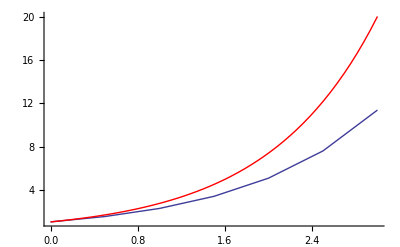

```mathematica
ff[h_,xmax_]:=NestList[{#1⟦1⟧+h,#1⟦2⟧+h #1⟦2⟧}&,{0,1},Floor[xmax/h]]
pap=ListPlot[ff[0.5,3],Joined->True];
pex=Plot[ⅇ^x,{x,0,3},PlotStyle->RGBColor[1,0,0]];
Show[pap,pex]
```

Euler's method neglects terms in h^2, and it is therefore known as a first-order method (in general, an n-th order method has an error term which varies as h^(n+1)).

Note that although most of the update schemes in these notes have been written as pure functions, there is no reason why they could not have used named functions. For example, this case could be coded as follows (note that we need to pass the step length to the function, which we have done here by iterating on a list of three items, so to recover just the (x,y) pairs we Map Most onto the result).

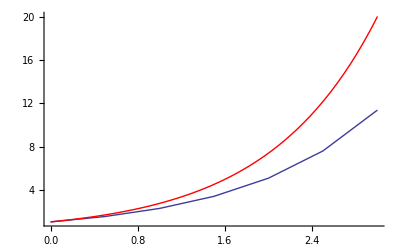

```mathematica
upd[{x_,y_,h_}]:={x+h,y+ h y,h}
ff[h_,xmax_]:=Map[Most,NestList[upd,{0,1,h},Floor[xmax/h]]]
pap=ListPlot[ff[0.5,3],Joined->True];
pex=Plot[ⅇ^x,{x,0,3},PlotStyle->RGBColor[1,0,0]];
Show[pap,pex,PlotRange->All]
```

### Euler predictor-corrector method

We established before that the approximation to the derivatives on which the simple Euler method was based is accurate only to first order in the step length. The basic problem is that it uses a one-sided (forward) difference scheme. The idea of the predictor-corrector method is to make an estimate of the value of y(x+h) using the first-order scheme, but then to correct it by using that estimate to make an improved estimate of the slope by using the average of the slopes at the start of the step and the predicted end of the step. The algorithm, then is 
 a) predictor step    Y(x+h) = y(x) + h f(x, y(x))
 b) corrector step    y(x+h) = y(x) + h/2 {f(x,y(x))+f(x+h,Y(x+h))}.
 It is worth noting that this predictor-corrector idea has been developed by Adams, Moulton and others into a very sophisticated range of algorithms, which rely on fitting polynomials (which may be of very high order) through the calculated values and basing corrections on those.  Mathematica's NDSolve function, for example, uses Adams methods of up to 12th order.
   The penalty with this Euler predictor-corrector method is that it requires one more function evaluation per step. The advantage, however, is that it is accurate to second order in the step length. Rather than prove this algebraically, we shall try to demonstrate it numerically.  
    Note that in our problem the algorithm may be simplified, as
     a) predictor step    Y(x+h) = y(x) + h y(x)
     b) corrector step    y(x+h) = y(x) + h/2 {f(x,y(x))+f(x+h,Y(x+h))}
= y(x) +h/2 {y(x)+y(x)+h y(x)} .

    Now we find we can achieve a broadly acceptable solution even with a step length as large as 0.5.

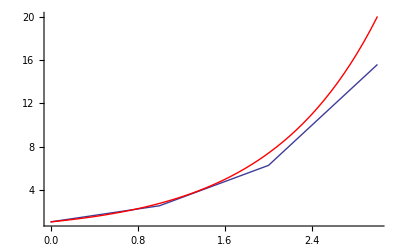

```mathematica
ff[h_,xmax_]:=NestList[{#1⟦1⟧+h,#1⟦2⟧+0.5 h (2 #1⟦2⟧+h #1⟦2⟧)}&,{0,1},Floor[xmax/h]]
pap=ListPlot[ff[1.,3],Joined->True];
pex=Plot[ⅇ^x,{x,0,3},PlotStyle->RGBColor[1,0,0]];
Show[pap,pex]
```

### The Runge-Kutta method

The names of Runge and Kutta are associated with a family of methods, of which the four-step method is typical. It requires four function evaluations per step, but is fourth-order accurate. The process defines four increments, based on the slope at the beginning of the step, two different estimates of the slope at the mid-point, and the slope at the end point, and combines them in the ratio 1:2:2:1. The algebra behind this is tedious, but the basic idea is that by adding up the right combination of terms the error terms can be eliminated order by order. The basic Euler method is first-order accurate, but combining two slightly different first-order schemes we can eliminate the term in h^2, with three we can eliminate the h^3 term, and with 4 we can eliminate the h^4 term.   
  δ_1= h f(x,y)
  δ_2= h f(x+1/2 h,y+1/2 δ_1)
  δ_3= h f(x+1/2 h,y+1/2 δ_2)
  δ_4= h f(x+h,y+δ_3)
  y(x+h)=y(x)+1/6(δ_1+ 2 δ_2 + 2 δ_3 + δ_4)..
  Again there are considerable simplifications for our chosen problem:

```mathematica
Clear[h]
δ1=h y;
δ2=h (y+δ1/2);
δ3=h (y+δ2/2);
δ4=h (y+δ3);
δ=1/6(δ1+2δ2+2δ3+δ4)//Simplify
```

1/24 h (24+12 h+4 h^2+h^3) y

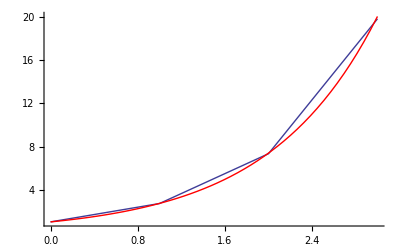

```mathematica
ff[h_,xmax_]:=NestList[{#1⟦1⟧+h,#1⟦2⟧+1/24 h (24+12 h+4 h^2+h^3) #1⟦2⟧}&,{0,1},Floor[xmax/h]]
pap=ListPlot[ff[1.,3],Joined->True];
pex=Plot[ⅇ^x,{x,0,3},PlotStyle->RGBColor[1,0,0]];
Show[pap,pex]
```

We can see a clear improvement over the Euler predictor-corrector method. We even obtain a sensible result now with a step length of 1.

### The thermal conduction equation

The equation for the one-dimensional flow of heat in a bar of cross-sectional area A and thermal conductivity κ relates the heat flow Q to the gradient of the temperature θ by
   Q=-κ A dθ/dx.
   The assumption of one-dimensional flow means that the edges of the bar are perfectly insulated. Suppose the cross-section in the bar, 1 metre long, varies according to
   A=π ((2-x)/100)^2  ,
   and the temperature θ=500K at x = 0 and θ=300K at x = 1m.

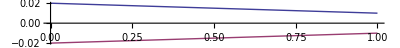

```mathematica
Plot[{(2-x)/100,(x-2)/100},{x,0,1},AspectRatio->0.1]
```

Now this is a slightly unusual case: as this is a first-order differential equation we need only one boundary condition, whereas we are given two boundary conditions and there is an unknown quantity, Q, in the equation. We explore two rather different methods of tackling this problem. Before we go on, it is worth noting that this equation has the same form as the diffusion equation, which describes the spreading of material down a concentration gradient.

#### The shooting method

We can think of this method as requiring us to take an initial guess at the heat transprt, Q, plug that into the equation, solve it using the boundary condition at x=0, looking at the value of θ at x=1, and then adjusting Q until we achieve the right value of θ at x=1. The analogy with artillery is that Q is some parameter of the system (in the analogy, the angle of elevation of the gun barrel) which is adjusted until the target is hit. This breaks the problem down into two steps -- solving the differential equation numerically and adjusting the parameter to satisfy the second boundary condition.

  We start by setting up a simple Euler method to solve the differential equation for some Q. In fact, of course, we can collapse Q/κ into one single parameter. Note that all we need to keep from the solution is the value of the temperature at the end-point.

```mathematica
esol[Qk_,h_,xmax_]:=Nest[{#[[1]]+h,#[[2]] - h(Qk (100/(2-#[[1]]))^2/π)}&,{0,500},Floor[xmax/h]][[2]]
```

```mathematica
esol[.1,.1,1]
```

352.318

```mathematica
Qsol=FindRoot[esol[Qk,.1,1]-300,{Qk,.1}]
```

{Qk→0.135427}

As a check, we'll plot the resulting temperature distribution

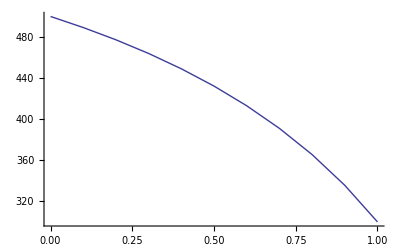

```mathematica
ListPlot[NestList[{#1⟦1⟧+h,#1⟦2⟧-(h (Qk (100/(2-#1⟦1⟧))^2))/π}/.Qsol/.h->0.1&,{0,500},Floor[1./0.1]],Joined->True,PlotRange->All]
```

It's worth exploring the solution to see whether the choice of step length makes any significant difference: try 0.1 and 0.01.

#### The linear equation method

An alternative approach to this problem avoids finding the heat flow by reformulating the problem in terms of continuity of heat flow. The fact that the bar is insulated means that if we divide the bar into N equal lengths, and write θ_i for the temperature at point i, where the cross-sectional area is A_i, the total heat flow must be the same at all points. In particular,
A_i(dθ/dx)_i=A_(i+1)(dθ/dx)_(i+1).

Now apply a centred-difference formula, based on the mid-points, and apply it to
A_(i-1/2)(dθ/dx)_(i-1/2)=A_(i+1/2)(dθ/dx)_(i+1/2). This gives
A_(i-1/2)(θ_i-θ_(i-1))=A_(i+1/2)(θ_(i+1)-θ_i).
If we insert the explicit form for the area and rearrange, we have

```mathematica
leq=((Subscript[A, i-1/2](Subscript[θ, i]-Subscript[θ, i-1])==Subscript[A, i+1/2](Subscript[θ, i+1]-Subscript[θ, i]))/.Subscript[A, j_]->π ((2-(j-1)h)/100)^2)//FullSimplify
```

(4+h (3-2 i))^2 θ_(-1+i)+(4+h-2 h i)^2 θ_(1+i)==2 (16+h (16+5 h-8 (2+h) i+4 h i^2)) θ_i

```mathematica
leq/.i->2
```

(4-h)^2 θ_1+(4-3 h)^2 θ_3==2 (16+h (16+21 h-16 (2+h))) θ_2

Now we can set up a system of equations, in which we substitute values for i running from 2 to N-1, as well as the known values of θ_1 and θ_N, and solve the N-2 equations for the N-2 variables. For example, with N=10

```mathematica
nN=10;
thsol=Solve[Table[leq/.h->1./(nN-1)/.i->j,{j,2,nN-1}]/.Subscript[θ, 1]->500/.Subscript[θ, 10]->300,Table[Subscript[θ, i],{i,2,nN-1}]]
```

{{θ_2→488.224,θ_3→474.977,θ_4→459.966,θ_5→442.812,θ_6→423.024,θ_7→399.943,θ_8→372.672,θ_9→339.961}}

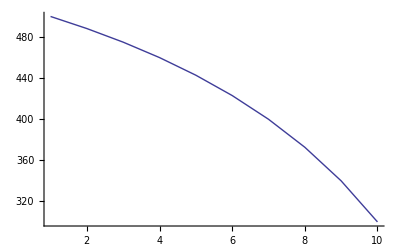

```mathematica
ListPlot[Append[Prepend[Table[Subscript[θ, i],{i,2,nN-1}]/.thsol⟦1⟧,500],300],Joined->True]
```

If we think a bit more carefully about the structure of the equations, we can see that each equation links the value of θ at one step to the values on each side. This means that we could rewrite the problem as a matrix equation. If the series of equations is written as follows, with the subscripts (n,m) denoting (equation number, grid position) there are N grid positions, at 2 of which the temperature is known, so that there are N-2 equations which might be written as
  c_(1,1) θ_1+c_(1,2) θ_2+c_(1,3) θ_3=0
c_(2,1) θ_2 +c_(2,2) θ_3 +c_(2,3) θ_4=0
...
c_(N-2,N-2) θ_(N-2) +c_(N-2,N-1) θ_(N-1) +c_(N-2,N) θ_N=0 
  and we know θ_1 and θ_N, so we can rearrange the equations as
  (c_(1,2) | c_(1,3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
c_(2,1) | c_(2,2) | c_(2,3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c_(3,1) | c_(3,2) | c_(3,3) | 0 | 0 | 0 | 0 | 0 | 0
0 | . | . | . | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | . | . | . | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | . | . | . | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | c_(N-3,N-2) | c_(N-3,N-2) | c_(N-3,N-1)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | c_(N-2,N-2) | c_(N-2,N-1))(θ_2
θ_3
θ_4
.
.
.
.
.
θ_(N-2)
θ_(N-1))=(-c_(1,1) θ_1
0
0
0
.
.
0
0
0
-c_(N-2,N) θ_N).
   
  This form of matrix, a so-called tridiagonal matrix, is particularly easy to solve. Tridiagonal matrices crop up so frequently in numerical applications that there was a special add-on package in Mathematica (up to version 5.2), LinearAlgebra`Tridiagonal`, to solve problems of this kind with great efficiency. It has now been superseded by the general purpose built-in function SparseArray. For any serious application, the sensible course would be to set up the problem in matrix form.

## Solving systems of equations

Problems involving several coupled equations are common in physics and other fields. Sometimes they occur naturally, as in electromagnetism where Maxwell's equations link electric and magnetic fields together, and sometimes they result from rewriting higher-order differential equations as coupled first-order equations. An example of the latter is the motion of a particle under the influence of a force. Instead of a second-order equation for the position x of the particle
m ẍ = F ,
we can work in terms of position and velocity,
m v̇= F ,
ẋ= v. 
This has the advantage that first-order equations are often rather easier to solve. Of course, it does not make any difference to the number of boundary conditions we need to specify -- instead of a value and slope of x (or two values of x), we need to specify a value of x and a value of v. 
  It is inevitable that dealing with systems of equations will require us to write our equations as lists, but apart from that there is little difference between this situation and the ones we have already met. In fact, the Runge-Kutta method we code above can be used with very little modification.
    Let's take the trivial case of simple harmonic motion. Here
m ẍ = -k x 
becomes
m v̇= -k x ,
ẋ= v. ,
or in Mathematica form using the forward Euler method

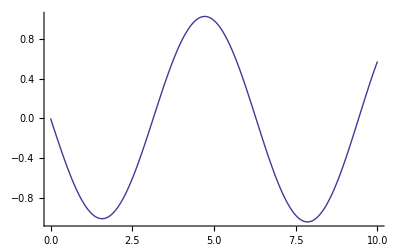

```mathematica
ff[k_,m_,Δt_,tmax_,v0_,x0_]:=NestList[{#1⟦1⟧+Δt,#1⟦2⟧-(k Δt #1⟦3⟧)/m,#1⟦3⟧+Δt #1⟦2⟧}&,{0,v0,x0},Floor[tmax/Δt]]
pap=ListPlot[Transpose[Drop[Transpose[ff[1.,1.,0.01,10,0,1.]],-1]],Joined->True]
```

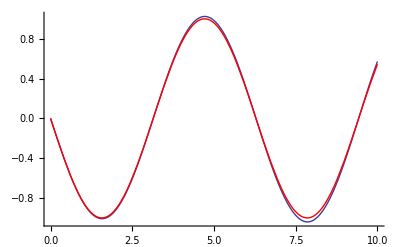

```mathematica
pex=Plot[-Sin[t],{t,0,10},PlotStyle->RGBColor[1,0,0]];
Show[pap,pex]
```

That is not bad, but if we run on for many more time steps we may see problems.

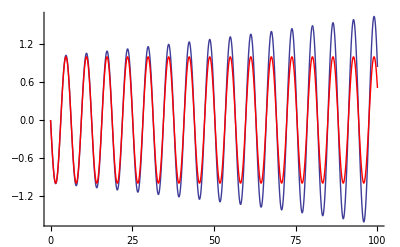

```mathematica
ff[k_,m_,Δt_,tmax_,v0_,x0_]:=NestList[{#1⟦1⟧+Δt,#1⟦2⟧-(k Δt #1⟦3⟧)/m,#1⟦3⟧+Δt #1⟦2⟧}&,{0,v0,x0},Floor[tmax/Δt]]
pap=ListPlot[Transpose[Drop[Transpose[ff[1.,1.,0.01,100,0,1.]],-1]],Joined->True];
pex=Plot[-Sin[t],{t,0,100},PlotStyle->RGBColor[1,0,0]];
Show[pap,pex]
```

Clearly our algorithm does not conserve energy with this time step, though with a timestep of 0.001 things are much better. We shall briefly return to this point about conserved quantities in the next lecture.

Similarly, any of the other algorithms we have discussed can be applied to systems of equations as well as to single equations.

### Stiff systems

Sometimes apparently quite innocent equations can give problems. Consider the pair of equations
ⅆu/ⅆt= 998 u +1998 v
ⅆv/ⅆt= -999 u -1999 v
with boundary conditions u(0)=2 and v(0)=-1, and try to solve the equations using our explicit Euler scheme. First, let's see what the analytic result is:

```mathematica
DSolve[{u'[t]==998 u[t]+1998 v[t],v'[t]==-999 u[t]-1999 v[t],u[0]==2,v[0]==-1},{u[t],v[t]},t]
```

{{u[t]→2 ⅇ^-t,v[t]→-ⅇ^-t}}

That seems fairly simple, so let's try a timestep of 0.01, and solve up to t=1.

```mathematica
fst[Δt_,tmax_,u0_,v0_]:=NestList[{#1⟦1⟧+Δt,#1⟦2⟧+998 Δt #1⟦2⟧+1998 Δt #1⟦3⟧,#1⟦3⟧-999 Δt #1⟦2⟧-1999 Δt #1⟦3⟧}&,{0,u0,v0},Floor[tmax/Δt]]
pap=ListPlot[Transpose[Drop[Transpose[fst[0.01,1,2.,-1.]],-1]],Joined->True]
```

-Graphics-

This is clearly a total disaster. Why? To answer that, consider the general analytic solution:

```mathematica
DSolve[{u'[t]==998 u[t]+1998 v[t],v'[t]==-999 u[t]-1999 v[t],u[0]==u0,v[0]==v0},{u[t],v[t]},t]//FullSimplify
```

{{u[t]→2 ⅇ^-t (u0+v0)-ⅇ^(-1000 t) (u0+2 v0),v[t]→-ⅇ^-t (u0+v0)+ⅇ^(-1000 t) (u0+2 v0)}}

What this shows us is that the general solution contains two components, one of which varies much more rapidly than the solution of the problem which we are actually interested in. Let's see if we can cure the problem by decreasing the time step further.

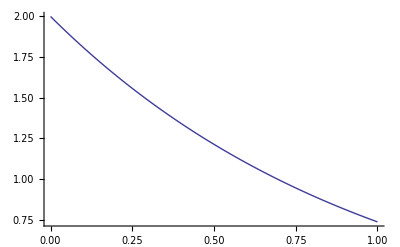

```mathematica
fst[Δt_,tmax_,u0_,v0_]:=NestList[{#1⟦1⟧+Δt,#1⟦2⟧+998 Δt #1⟦2⟧+1998 Δt #1⟦3⟧,#1⟦3⟧-999 Δt #1⟦2⟧-1999 Δt #1⟦3⟧}&,{0,u0,v0},Floor[tmax/Δt]]
pap=ListPlot[Transpose[Drop[Transpose[fst[0.001,1,2.,-1.]],-1]],Joined->True]
```

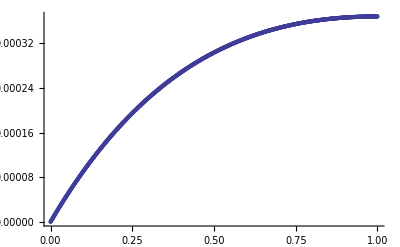

```mathematica
est=fst[.001,1,2.0,-1.0];
diff=Map[{#[[1]],2 Exp[-#[[1]]]-#[[2]]}&,est];ListPlot[diff]
```

The message, then, is that if our problem contains elements with very different time scales, if we try to solve explicitly we have to set the time-step to follow the most rapidly varying part of the problem. Problems with very different time scales are known as stiff problems. This case, in which the scales differ by a factor of 1000, is relatively mild: enormously stiff problems occur in cases in which diffusion and drift (motion of a charged particle in an electric field) occur together.

In this situation, as in many others, we can restore stability by using an implicit scheme - that is, one in which we have an equation to solve for the updated value rather than obtaining an explicit form. Implict schemes will be explored in the next lecture and in one of the exercises in the homework.

## Summary

Of course this brief discussion has had to leave a lot out. In any `black box' implementation of a numerical solver there is usually an algorithm for altering the step size automatically. For nice smooth functions the step size can then grow to quite large values -- and then one has to build in algorithms to recognise when something has changed suddenly (in a heat flow problem something might have melted and suddenly changed its thermal conductivity or specific heat).  Another refinement is to recognise that for a sufficiently smooth function the true function is probably approached in some smooth way as the step size is reduced -- so-called Bulirsch-Stoer methods use this idea to fit the function being evaluated to a function of the step size, and then evaluate it at a step size of zero. General-purpose codes may have a variety of methods at their disposal (have a look at the documentation of the methods in the Mathematica NDSolve routine, for example: in 1996 it said there that the code for NDSolve was 500 pages long, and by 2009 it had grown to 1400 pages long!).

A.H. Harker
Physics and Astronomy, UCL
September 2005, updated January 2009, January 2011, January 2012.
Amended by Patrick Guio, Physics and Astronomy, UCL, January 2015 and January 2017.